# Simple DSolve Example

## by Prof. Lee Bardwell, Univ. of Calif., Irvine version 11 Jan 2018

```mathematica
ClearAll["Global`*"]

(* defining the system - simple exponential decay of Y *)
system1 = {
Y'[t] == -k Y[t], Y[0]==Yzero
};

(* getting the exact symbolic solution *)solution1 = DSolve[system1,Y[t],t]
```

{{Y[t]→ⅇ^(-k t) Yzero}}

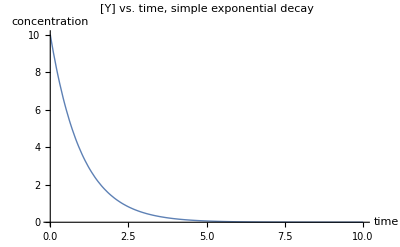

```mathematica
(* plotting the solution *)
parameters1 = {k->1,Yzero-> 10};
case1 =solution1/.parameters1;

Plot[{Y[t]/.case1},{t,0,10},PlotStyle->Thick,PlotRange->{0,10},AxesLabel->{"time","concentration"},PlotLabel->"[Y] vs. time, simple exponential decay"]
```

```mathematica
(* getting the value of Y at at particular time, in this case, t = 2 *)
Y[t]/.case1/.t-> 2.0
```

{1.35335}

Manipulating the solution

```mathematica
(* Manipulating the solution *)
(* Using this method we can leave both the system and the DSolve call outside of Manipulate, but we need to use "dummy variables" (such as kValue, below) for the parameters we want to manipulate *)

Manipulate[
parameters2= {k->kValue,Yzero-> 10};
Plot[{Y[t]/.solution1/.parameters2},{t,0,20},PlotStyle->Thick,PlotRange->{-0.2,10},AxesLabel->{"time","concentration"},PlotLabel->"[Y] vs. time, simple exponential decay"],
{kValue,0.2,10}
]
```

```mathematica
(* Another format for Manipulating the solution *)
(* For this method, both the system and the DSolve call need to be inside Manipulate, but we don't need to use dummy variables *)

Manipulate[
system2 = {
Y'[t] == -k Y[t], Y[0]==Yzero
};
solution2 = DSolve[system2,Y[t],t];
Plot[{Y[t]/.solution2},{t,0,20},PlotStyle->Thick,PlotRange->{-0.2,10},AxesLabel->{"time","concentration"},PlotLabel->"[Y] vs. time, simple exponential decay"],
{{k,0.2},0,10},
{{Yzero,10},0,10}
]
```

```mathematica
(* Another format for Manipulating the solution *)
(* Since DSolve gave us the exact solution, we just use this *)

Manipulate[
Plot[ⅇ^(-k t) Yzero,{t,0,20},PlotStyle->Thick,PlotRange->{-0.2,10},AxesLabel->{"time","concentration"},PlotLabel->"[Y] vs. time, simple exponential decay"],
{{k,0.2},0,10},
{{Yzero,10},0,10}
]
```

```mathematica
(* Yet another format for Manipulating the solution *)
(* First we set up a function based on the exact solution *)

(* set up the function *)
expDecay[Yzero_,k_,t_]:=ⅇ^(-k t) Yzero;

(* use the function *)
expDecay[10,0.2,3.5]
```

4.96585

```mathematica
(* Then we manipulate a plot of the function *)
(* Again, we don't need dummy variables *)

Manipulate[
Plot[expDecay[Yzero,k,t],{t,0,20},PlotStyle->Thick,PlotRange->{-0.2,10},AxesLabel->{"time","concentration"},PlotLabel->"[Y] vs. time, simple exponential decay"],
{{k,0.2},0,10},
{{Yzero,10},0,10}
]
```